```mathematica
Quit[];
```

# Ploop FFTlog

Alejandro Aviles
avilescervantes@gmail.com

Compute the matter 1-loop real space power spectrum as in 1708.08130. (Massless neutrino kernels)

The most expensive part is the computation of the M22 matrix (about two seconds). But M22 is cosmology independent and can be stored in a table.

```mathematica
SetDirectory[NotebookDirectory[]];
<<modules.m

(* input liner power spectrum *)
(*No headers. Two file column {k[h/Mpc], Pk[(Mpc/h)^3]} *)
inputfilename="./pk_cb_m04_z05.dat";
inputpkT=Import[inputfilename];  
inputpk=Interpolation[inputpkT];
inkT=inputpkT[[All,1]];

(*Output Ploop *)
kminout=0.001;
kmaxout=1;
Nkout=100;
kTout=Table[kminout Exp[(i-1)Log[kmaxout/kminout]/(Nkout-1)],{i,1,Nkout}];


(* Parameters for FFTLog *)
kmin=10.*10^(-5);
kmax=10.;
Nfftlog=256;
biasnu=-0.3;  (* -3<biasnu<-1, biasnu>-1 *)
```

## Compute M22 and M13 matrices

Since these matrices are independent of the cosmology, this can be done just one time and store it in a file.

```mathematica
AbsoluteTiming[M22matrix=M22M[kmin,kmax,Nfftlog,biasnu];]
Dimensions[M22matrix]
AbsoluteTiming[M13vector=M13M[kmin,kmax,Nfftlog,biasnu];]
Dimensions[M13vector]
```

{2.30524,Null}

{257,257}

{0.00365,Null}

{257}

## main

```mathematica
ta=AbsoluteTime[];

cmTetamT=cmTetamTM[inputpkT,kmin,kmax,Nfftlog,biasnu];
cmT=cmTetamT[[All,1]];
etamT=cmTetamT[[All,2]];

If[biasnu>-1,P13T=P13UVM[kTout,cmT,etamT,biasnu,M13vector,inputpkT];]
If[biasnu<-1,P13T=P13IRM[kTout,cmT,etamT,biasnu,M13vector,inputpkT];]
P22T=P22M[kTout,cmT,etamT,biasnu,M22matrix];
AbsoluteTime[]-ta;

Print["Time = ", AbsoluteTime[]-ta, " seconds"]
```

Time = 0.12555 seconds

## Export

```mathematica
Export["P22T.dat",P22T]
Export["P13T.dat",P13T]
```

P22T.dat

P13T.dat

## Plot

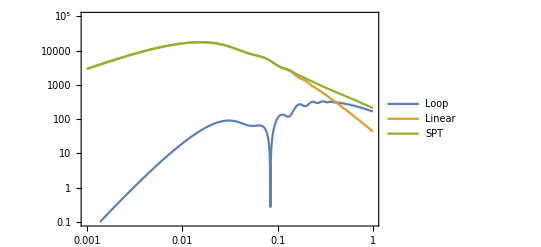

```mathematica
pkl=Interpolation[inputpkT];
P22=Interpolation[P22T];P13=Interpolation[P13T];
Ploop[k_]:=P22[k]+P13[k];
LogLogPlot[{Abs[Ploop[k]],pkl[k],pkl[k]+Ploop[k]},{k,0.001,1},PlotRange->{{0.001,1},{0.1,10^5}},Frame->True,PlotLegends->{"Loop","Linear","SPT"}, ImageSize->400]
```